## φ介子

### 零宽度基态

#### 确定共振态贡献

{14.945,Null}

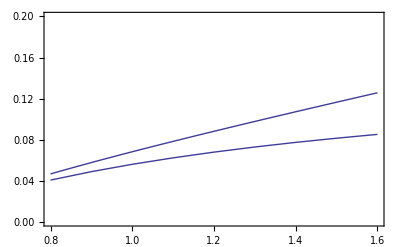

```mathematica
Clear[a, pts, plotsub, plotfull]
Λ=0.1; s0=1.95; up=13; 
a[M2_]:=(4π)/9 1/Log[M2/Λ^2]
f1[M2_]:=M2/(4π)(1+a[M2]/π-0.225 0.6/M2(a[M2]/0.7)^(8/9)-0.4(0.6/M2)^2-0.14(0.6/M2)^3)
f2[M2_]:=M2^2/(4π)(1+a[M2]/π+0.4(0.6/M2)^2+0.28(0.6/M2)^3)
cont[M2_]:=9∫_s0^up 1/(36π)(1+a[s]/π)E^(-s/M2)ⅆs//N
contsubtract[M2_]:=f1[M2]-cont[M2]

Timing[
pts = Table[contsubtract[M2],{M2,0.8,1.6, 0.1}] ;
]
plotsub=ListLinePlot[Transpose[Join[{Range[0.8, 1.6, 0.1]}, {pts}]]];
plotfull=Plot[f1[M2],{M2,0.8, 1.6}];
Show[{plotsub, plotfull},PlotRange->{{0.8,1.6},{0.,0.2}}, 
AxesOrigin->{0.5,0.8}, Frame->True, Axes->False]
```

#### 确定合适的M^2的范围

首先高阶修正小于总贡献的30%。

```mathematica
FindRoot[Abs[(-0.225 0.6/M2(a[M2]/0.7)^(8/9)-0.4(0.6/M2)^2-0.14(0.6/M2)^3)/(1+a[M2]/π-0.225 0.6/M2(a[M2]/0.7)^(8/9)-0.4(0.6/M2)^2-0.14(0.6/M2)^3)]==0.3,{M2,1}]
```

{M2→0.969063}

其次连续谱贡献小于总贡献的30%。

```mathematica
Timing[
Table[cont[M2]/f1[M2],
	{M2, 0.9, 1.8, 0.1}]
]
```

{16.567,{0.153273,0.178893,0.204587,0.229847,0.254375,0.277999,0.300621,0.322195,0.342706,0.362159}}

这里选取M2为 [1.0, 1.5]

#### 拟合出基态质量和耦合常数

耦合常数的实验值为(g_φ^2/(4π))_exp=11.7±0.9，即g→12.13 。
φ介子质量实验值为m_φ=1.019455±0.020。
m2→1.04

```mathematica
Clear[ptsphi, dataphi, dM2, g2, m2]
M2min=1.0; M2max=1.5; dM2=0.05;
Timing[
ptsphi = Table[contsubtract[M2],{M2, M2min, M2max, dM2}] ;
]
dataphi = Transpose[Join[{Range[M2min, M2max, dM2]}, {ptsphi}]];
FindFit[dataphi, 9π m2/g2 E^(-m2/M2),{g2,m2},M2]
{√g2, √m2}/.%
```

{18.252,Null}

{g2→183.61,m2→1.11489}

{13.5503,1.05588}

#### 画出基态贡献

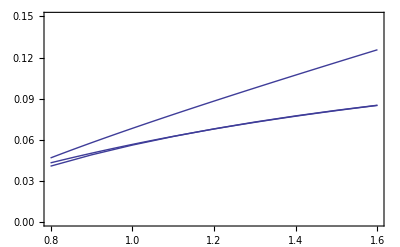

```mathematica
Clear[g2, m2]
res[M2_]:=9(π m2)/g2 E^(-m2/M2)/.{g2->183.20959561249822,m2->1.0873216462268602}
plotres = Plot[res[M2], {M2, 0.8, 1.6}];
Show[{plotsub, plotfull, plotres},PlotRange->{{0.8,1.6},{0.,0.15}}, 
AxesOrigin->{0.5,0.8}, Frame->True, Axes->False]
```

### 零宽度基态和有宽度激发态

s0设定为3.0

#### 确定共振态贡献

{17.191,Null}

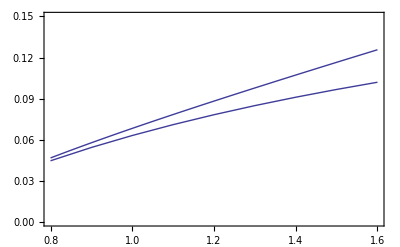

```mathematica
Clear[pts, plotsub, plotfull]
Λ=0.1; s0=2.8; up=13;
a[M2_]:=(4π)/9 1/Log[M2/Λ^2]
f1[M2_]:=M2/(4π)(1+a[M2]/π-0.225 0.6/M2(a[M2]/0.7)^(8/9)-0.4(0.6/M2)^2-0.14(0.6/M2)^3)
f2[M2_]:=M2^2/(4π)(1+a[M2]/π+0.4(0.6/M2)^2+0.28(0.6/M2)^3)
contphi[M2_]:=9∫_s0^up 1/(36π)(1+a[s]/π)E^(-s/M2)ⅆs//N
contsubtractphi[M2_]:=f1[M2]-contphi[M2]

Timing[
pts = Table[contsubtractphi[M2],{M2,0.8,1.6, 0.1}] ;
]
plotsub=ListLinePlot[Transpose[Join[{Range[0.8, 1.6, 0.1]}, {pts}]]];
plotfull=Plot[f1[M2],{M2,0.8, 1.6}];
Show[{plotsub, plotfull},PlotRange->{{0.8,1.6},{0.,.15}}, 
AxesOrigin->{0.5,0.8}, Frame->True, Axes->False]
```

#### 确定合适的M^2的范围

首先高阶修正小于总贡献的20%。

```mathematica
FindRoot[Abs[(-0.225 0.6/M2(a[M2]/0.7)^(8/9)-0.4(0.6/M2)^2-0.14(0.6/M2)^3)/(1+a[M2]/π-0.225 0.6/M2(a[M2]/0.7)^(8/9)-0.4(0.6/M2)^2-0.14(0.6/M2)^3)]==0.2,{M2,1}]
```

{M2→1.15282}

其次连续谱贡献小于总贡献的20%。

```mathematica
Timing[
Table[contphi[M2]/f1[M2],{M2, 1.2, 1.9, 0.1}]
]
```

{13.728,{0.112811,0.131841,0.150966,0.169978,0.188714,0.207056,0.224912,0.242216}}

M2选取为[1.2, 1.7]

#### 拟合出基态和激发态质量和耦合常数

φ介子质量实验值为m_φ=1.119455±0.000020，宽度Γ=0.00426±0.00004，
耦合常数的实验值为(g_φ^2/(4π))_exp=11.7±0.9，即g→12.13 。
m2→1.25 ； g2→147。

φ介子激发态质量实验值为m_φ'=1.680±0.020，宽度Γ=0.150±0.050。

```mathematica
Clear[ptsphi, dataphi, dM2]
M2min=1.2; M2max=1.7; dM2=0.02;
smin=2.5; smax=3.4;
Timing[
ptsphi = Table[contsubtractphi[M2],{M2, M2min, M2max, dM2}] ;
]
dataphi = Transpose[Join[{Range[M2min, M2max, dM2]}, {ptsphi}]];
FindFit[dataphi, 9π m2/g2 E^(-m2/M2)+9 Re[∫_smin^smax frhop(Γ mprime)/((s-mprime^2)^2+Γ^2 mprime^2)E^(-s/M2)ⅆs]
	,{{g2,100},{m2,1}, frhop, mprime, Γ}, M2]
```

{44.679,Null}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{g2→160.685,m2→1.25386,frhop→0.0864846,mprime→0.0182385,Γ→4.86494}

#### 零宽度激发态

```mathematica
FindFit[dataphi, 9π m2/g2 E^(-m2/M2)+9π mp2/gp2 E^(-mp2/M2)
	,{{g2,100}, {m2,0.5}, gp2, {mp2,1.1}}, M2]
{√m2, √mp2}/.%
```

{g2→6.24147×10^6,m2→0.350162,gp2→159.238,mp2→1.27076}

{0.591745,1.12728}

```mathematica
FindFit[dataphi, 9π m2/g2 E^(-m2/M2)+9π mp2/gp2 E^(-mp2/M2)/.{g2->147, m2->1.25}
	,{{gp2,100}, {mp2,1.3}}, M2]
{√gp2, √mp2}/.%
```

{gp2→-1863.97,mp2→0.994568}

{0.+43.1737 ⅈ,0.99728}

#### 画出基态贡献

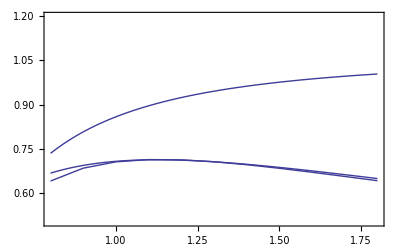

```mathematica
Clear[g2, m2]
res[M2_]:=9(π m2)/g2 E^(-m2/M2)/.{g2->183.6646955008578,m2->1.127119671544122}
plotres = Plot[4 π/M2 res[M2], {M2, 0.8, 2.5}];
Show[{plotsub, plotfull, plotres},PlotRange->{{0.8,2.5},{0.5,1.2}}, 
AxesOrigin->{0.5,0.8}, Frame->True, Axes->False]
```